## Definitions of functions

```mathematica
ClearAll["Global`*"]
```

eqnVars[eqn] lists the variables in the equation eqn.

```mathematica
eqnVars[eqn_]:=Variables[Subtract @@ eqn];
```

varsPositive[{x,y,z}] outputs x>0 && y>0 && z>0.  This condition restricts the variables to positive values.

```mathematica
varsPositive[vars_]:=And @@ Map[#>0&,vars];
```

eqnResolve[eqn,vars,cond] attempts to determine whether the Diophantine equation eqn with variables vars has any positive solutions that satisfy the condition cond.

```mathematica
eqnResolve[eqn_,vars_,cond_:True] :=
 Resolve[Exists[vars, eqn && varsPositive[vars] && cond], Integers];
```

eqnFindInstance[eqn,vars,cond] attempts to find one positive solution to the Diophantine equation eqn with variables vars that satisfies the condition cond.

```mathematica
eqnFindInstance[eqn_,vars_,cond_:True] :=
 vars/.Flatten[FindInstance[eqn && varsPositive[vars] && cond,vars, Integers]];
```

solSmallerCondition[{1,2,3},{x,y,z}] outputs (x<1|y<2||z<3)&&(x≤1&&y≤2&&z≤3).  This condition defines a solution smaller than {1,2,3}.

```mathematica
solSmallerCondition[sol_,vars_]:=
 Or@@MapThread[#1<#2&,{vars,sol}] && And@@MapThread[#1≤#2&,{vars,sol}];
```

Assuming that a solution exists, eqnFindSmallestSolution[eqn,vars,cond] attempts to find the smallest positive solution to the Diophantine equation eqn with variables vars that satisfies the condition cond.

```mathematica
eqnFindSmallestSolution[eqn_,vars_,cond_:True]:=
 NestWhile[
  eqnFindInstance[eqn,vars,solSmallerCondition[#,vars]&&cond]&,
  eqnFindInstance[eqn,vars,cond],
  eqnResolve[eqn,vars,solSmallerCondition[#,vars]&&cond]&
 ];
```

Given a Diophantine equation eqn with variables vars, eqnFindSolutions[eqn,vars,f] attempts to find a smallest positive solution, if one exists.  If it can be shown that no solutions exist, then the string "No Solution" is output.  Otherwise, if it cannot be determined whether eqn has a positive solution, then f[eqn,vars] is output.  And if the argument f is omitted, then f is assumed to be the constant function that outputs the string "Unknown".

```mathematica
eqnFindSolutions[eqn_, vars_, f_:("Unknown"&)] := 
 Switch[
  eqnResolve[eqn, vars], 
  True, 
  {eqn, Flatten[eqnFindSmallestSolution[eqn, vars]]},
  False,
  {eqn, "No Solution"},
  _,
  {eqn, f[eqn,vars]}
 ]
```

## 1. 2 x + 3y = n , n ∈ {1, ... , 15}

```mathematica
vars={x,y};
```

```mathematica
setofEqns = 2 x + 3 y== # &  /@ Range[1,15];
```

```mathematica
eqnFindSolutions[#, vars] & /@ setofEqns
```

{{x^2==1+y^2,No Solution},{x^2==1+2 y^2,{3,2}},{x^2==1+3 y^2,{2,1}},{x^2==1+4 y^2,No Solution},{x^2==1+5 y^2,{9,4}},{x^2==1+6 y^2,{5,2}},{x^2==1+7 y^2,{8,3}},{x^2==1+8 y^2,{3,1}},{x^2==1+9 y^2,No Solution},{x^2==1+10 y^2,{19,6}},{x^2==1+11 y^2,{10,3}},{x^2==1+12 y^2,{7,2}},{x^2==1+13 y^2,{649,180}},{x^2==1+14 y^2,{15,4}},{x^2==1+15 y^2,{4,1}},{x^2==1+16 y^2,No Solution},{x^2==1+17 y^2,{33,8}},{x^2==1+18 y^2,{17,4}},{x^2==1+19 y^2,{170,39}},{x^2==1+20 y^2,{9,2}}}

```mathematica
Grid[eqnFindSolutions[#, vars] & /@ setofEqns]
```

2 x+3 y==1 | No Solution
2 x+3 y==2 | No Solution
2 x+3 y==3 | No Solution
2 x+3 y==4 | No Solution
2 x+3 y==5 | {1,1}
2 x+3 y==6 | No Solution
2 x+3 y==7 | {2,1}
2 x+3 y==8 | {1,2}
2 x+3 y==9 | {3,1}
2 x+3 y==10 | {2,2}
2 x+3 y==11 | {4,1}
2 x+3 y==12 | {3,2}
2 x+3 y==13 | {5,1}
2 x+3 y==14 | {4,2}
2 x+3 y==15 | {6,1}

## 2. x^2 = y^2 + n , n ∈ {1, ... , 16}

```mathematica
vars={x,y};
```

```mathematica
setofEqns= x^2==y^2+  # &  /@ Range[1,16];
```

```mathematica
Grid[eqnFindSolutions[#, vars] & /@ setofEqns]
```

x^2==1+y^2 | No Solution
x^2==2+y^2 | No Solution
x^2==3+y^2 | {2,1}
x^2==4+y^2 | No Solution
x^2==5+y^2 | {3,2}
x^2==6+y^2 | No Solution
x^2==7+y^2 | {4,3}
x^2==8+y^2 | {3,1}
x^2==9+y^2 | {5,4}
x^2==10+y^2 | No Solution
x^2==11+y^2 | {6,5}
x^2==12+y^2 | {4,2}
x^2==13+y^2 | {7,6}
x^2==14+y^2 | No Solution
x^2==15+y^2 | {4,1}
x^2==16+y^2 | {5,3}

## 3. x^2 = n y^2 + 1 , n ∈ {1, ... , 20}

```mathematica
vars={x,y};
```

```mathematica
setofEqns= x^2== # y^2+ 1 &  /@ Range[1,20];
```

```mathematica
Grid[eqnFindSolutions[#, vars] & /@ setofEqns]
```

x^2==1+y^2 | No Solution
x^2==1+2 y^2 | {3,2}
x^2==1+3 y^2 | {2,1}
x^2==1+4 y^2 | No Solution
x^2==1+5 y^2 | {9,4}
x^2==1+6 y^2 | {5,2}
x^2==1+7 y^2 | {8,3}
x^2==1+8 y^2 | {3,1}
x^2==1+9 y^2 | No Solution
x^2==1+10 y^2 | {19,6}
x^2==1+11 y^2 | {10,3}
x^2==1+12 y^2 | {7,2}
x^2==1+13 y^2 | {649,180}
x^2==1+14 y^2 | {15,4}
x^2==1+15 y^2 | {4,1}
x^2==1+16 y^2 | No Solution
x^2==1+17 y^2 | {33,8}
x^2==1+18 y^2 | {17,4}
x^2==1+19 y^2 | {170,39}
x^2==1+20 y^2 | {9,2}

## 4. x^2 = y^3 + n , n ∈ {-20, ... , 20}

This is Mordell’s equation.

```mathematica
vars = {x,y};
```

```mathematica
setofEqns= x^2==y^3+ # &  /@ Range[-20,20];
```

For the following values of n, Mordell’s equation is known to have no solutions, according to https://oeis.org/A081121 and https://oeis.org/A054504 .

```mathematica
MordellNoSol = {-3, -5, -6, -9, -10, -12, -14, -16, -17, 6, 7, 11, 13, 14, 20};
```

And according to https://oeis.org/A001014/a001014.txt, all solutions when n=4, 5, 10, or 16 are non-positive.

```mathematica
MordellNonPos={4,5,10,16};
```

In addition, according to https://oeis.org/A081120, when n=-8 there is exactly one solution.  Evidently, this is the solution {x,y} = {0,2}, which is non-positive.

```mathematica
eqnMordellTest[eqn_, {x,y}]:=
 If[MemberQ[x^2==y^3+ # &  /@ Join[MordellNoSol, MordellNonPos, {-8}], eqn],"No Solution","Unknown"];
```

Now, to obtain our answers, we use the code below.

```mathematica
Grid[eqnFindSolutions[#, vars, eqnMordellTest] & /@ setofEqns]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

x^2==-20+y^3 | {14,6}
x^2==-19+y^3 | {18,7}
x^2==-18+y^3 | {3,3}
x^2==-17+y^3 | No Solution
x^2==-16+y^3 | No Solution
x^2==-15+y^3 | {7,4}
x^2==-14+y^3 | No Solution
x^2==-13+y^3 | {70,17}
x^2==-12+y^3 | No Solution
x^2==-11+y^3 | {4,3}
x^2==-10+y^3 | No Solution
x^2==-9+y^3 | No Solution
x^2==-8+y^3 | No Solution
x^2==-7+y^3 | {1,2}
x^2==-6+y^3 | No Solution
x^2==-5+y^3 | No Solution
x^2==-4+y^3 | {2,2}
x^2==-3+y^3 | No Solution
x^2==-2+y^3 | {5,3}
x^2==-1+y^3 | No Solution
x^2==y^3 | {1,1}
x^2==1+y^3 | {3,2}
x^2==2+y^3 | No Solution
x^2==3+y^3 | {2,1}
x^2==4+y^3 | No Solution
x^2==5+y^3 | No Solution
x^2==6+y^3 | No Solution
x^2==7+y^3 | No Solution
x^2==8+y^3 | {3,1}
x^2==9+y^3 | {6,3}
x^2==10+y^3 | No Solution
x^2==11+y^3 | No Solution
x^2==12+y^3 | {47,13}
x^2==13+y^3 | No Solution
x^2==14+y^3 | No Solution
x^2==15+y^3 | {4,1}
x^2==16+y^3 | No Solution
x^2==17+y^3 | {5,2}
x^2==18+y^3 | {19,7}
x^2==19+y^3 | {12,5}
x^2==20+y^3 | No Solution

## 5. x^2 = n y^3 + 1 , n ∈ {1, ... , 10}

This equation is a elliptic curve. This paper (https://doi.org/10.1112/jlms/s1-43.1.1) comprehensively overviews Diophantine Equations of the general form x^2==ay^3+by^2+cy+d. Our equation is a special case of the former, with a=n, b=0, c=0,and d=1. No external resources were found to explain why the original chart lists all of the present “Unknown” answers as "No Solution”.

```mathematica
vars = {x,y};
```

```mathematica
setofEqns= x^2== # y^3+ 1 &  /@ Range[1,10];
```

```mathematica
Grid[eqnFindSolutions[#, vars] & /@ setofEqns]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

x^2==1+y^3 | {3,2}
x^2==1+2 y^3 | Unknown
x^2==1+3 y^3 | {2,1}
x^2==1+4 y^3 | Unknown
x^2==1+5 y^3 | Unknown
x^2==1+6 y^3 | {7,2}
x^2==1+7 y^3 | Unknown
x^2==1+8 y^3 | {3,1}
x^2==1+9 y^3 | Unknown
x^2==1+10 y^3 | {9,2}

```mathematica
ContourPlot3D[ x^2== n y^3 +  1 ,{x,-10,10},{y,-10,10}, {n,-20,20}, PlotLegends->Placed[{"x^2== n*y^3 +  1"},Above]]
```

-Graphics3D-

## 6. x^3 = y^4 + n y x - 1 , n ∈ {-20, ... , 20}

Diophantine equations of this form are described in NKS: http://www.wolframscience.com/nks/notes-12-9--properties-of-diophantine-equations/:

	“ x^3==y^4+x y + a. For most values of a (including specifically a=1) the continuous version of this equation defines a surface of genus 3, 	so there are at most a finite number of integer solutions. (An equation of degree d generically defines a surface of genus (d-1)(d-2)/2.) 	Note that x^3 ==y^4+a is equivalent to x^3==z^2+a by a simple substitution.”

```mathematica
vars = {x,y};
```

```mathematica
setofEqns= x^3==y^4+ # y x - 1 &  /@ Range[-20,20];
```

Note that the table on page 790 of NKS contains a typographical error.  The smallest solution for x^3==y^4-12 x y-1 is {x,y}={2,3}, not {x,y}={3,2}.  In fact, {x,y}={3,2} is not even a solution for the equation.

The algorithm can find the solution {x^3==-1-9 x y+y^4,{80,27}} despite the solution being relatively large. In later sections of this notebook, some solutions become too large for FindInstance to find them.

```mathematica
Grid[eqnFindSolutions[#, vars] & /@ setofEqns]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

x^3==-1-20 x y+y^4 | {10,7}
x^3==-1-19 x y+y^4 | {3,4}
x^3==-1-18 x y+y^4 | {75,26}
x^3==-1-17 x y+y^4 | Unknown
x^3==-1-16 x y+y^4 | Unknown
x^3==-1-15 x y+y^4 | {624,125}
x^3==-1-14 x y+y^4 | Unknown
x^3==-1-13 x y+y^4 | Unknown
x^3==-1-12 x y+y^4 | {2,3}
x^3==-1-11 x y+y^4 | Unknown
x^3==-1-10 x y+y^4 | Unknown
x^3==-1-9 x y+y^4 | {80,27}
x^3==-1-8 x y+y^4 | {12,7}
x^3==-1-7 x y+y^4 | {1,2}
x^3==-1-6 x y+y^4 | {15,8}
x^3==-1-5 x y+y^4 | Unknown
x^3==-1-4 x y+y^4 | {30,13}
x^3==-1-3 x y+y^4 | Unknown
x^3==-1-2 x y+y^4 | Unknown
x^3==-1-x y+y^4 | Unknown
x^3==-1+y^4 | No Solution
x^3==-1+x y+y^4 | {1,1}
x^3==-1+2 x y+y^4 | {3,2}
x^3==-1+3 x y+y^4 | {5,3}
x^3==-1+4 x y+y^4 | {2,1}
x^3==-1+5 x y+y^4 | Unknown
x^3==-1+6 x y+y^4 | Unknown
x^3==-1+7 x y+y^4 | Unknown
x^3==-1+8 x y+y^4 | {20,9}
x^3==-1+9 x y+y^4 | {3,1}
x^3==-1+10 x y+y^4 | Unknown
x^3==-1+11 x y+y^4 | {5,2}
x^3==-1+12 x y+y^4 | Unknown
x^3==-1+13 x y+y^4 | Unknown
x^3==-1+14 x y+y^4 | Unknown
x^3==-1+15 x y+y^4 | Unknown
x^3==-1+16 x y+y^4 | {4,1}
x^3==-1+17 x y+y^4 | Unknown
x^3==-1+18 x y+y^4 | {8,3}
x^3==-1+19 x y+y^4 | Unknown
x^3==-1+20 x y+y^4 | Unknown

```mathematica
ContourPlot3D[ x^3 == y^4 + n y x - 1, {x, -10, 10}, {y, -10, 10}, {n, -100, 100}, AxesLabel -> True]
```

## 7. x^2 = y^5 + n y + 3 , n ∈ {0, ... , 9}

```mathematica
vars = {x,y};
```

```mathematica
setofEqns= x^2==y^5+ # y + 3  &  /@ Range[0,9];
```

As described in the table on page 790, the calculations that were performed for NKS were unable to determine whether the Diophantine equations x^2==3+4 y+y^5 and x^2==3+9 y+y^5 have positive solutions.  We show below that they have no solutions.

```mathematica
Grid[eqnFindSolutions[#, vars] & /@ setofEqns]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

x^2==3+y^5 | {2,1}
x^2==3+y+y^5 | {2537,23}
x^2==3+2 y+y^5 | Unknown
x^2==3+3 y+y^5 | Unknown
x^2==3+4 y+y^5 | No Solution
x^2==3+5 y+y^5 | {3,1}
x^2==3+6 y+y^5 | Unknown
x^2==3+7 y+y^5 | {7,2}
x^2==3+8 y+y^5 | Unknown
x^2==3+9 y+y^5 | No Solution

```mathematica
ContourPlot3D[ x^2==y^5+ n y + 3,{x,-10,10},{y,-10,10},{n,-100,100},AxesLabel->True]
```

## 8. x^3 + y^3 = z^2+ n , n ∈ {1, ... , 10}

```mathematica
vars = {x,y,z};
```

```mathematica
setofEqns= x^3 + y^3 == z^2 + #  &  /@ Range[1,10];
```

In this case, if eqnFindSolutions[eqn,{x,y,z}] returns "Unknown", we use eqnFindSmallestSolution to attempt to find a solution {x,y,z} with x<500, y<500, and z<5000.  Note that this calculation takes several minutes.

```mathematica
Grid[
 eqnFindSolutions[#, vars, eqnFindSmallestSolution[##,x<500 && y<500 && z<5000]&]&/@ setofEqns]
```

x^3+y^3==1+z^2 | {1,1,1}
x^3+y^3==2+z^2 | {107,232,3703}
x^3+y^3==3+z^2 | {1,3,5}
x^3+y^3==4+z^2 | {5,12,43}
x^3+y^3==5+z^2 | {2,1,2}
x^3+y^3==6+z^2 | {5,53,386}
x^3+y^3==7+z^2 | {2,2,3}
x^3+y^3==8+z^2 | {2,1,1}
x^3+y^3==9+z^2 | {7,3,19}
x^3+y^3==10+z^2 | {3,2,5}

```mathematica
Manipulate[ContourPlot3D[ x^3 + y^3 == z^2 + n,{x,-10,10},{y,-10,10},{z,-100,100},AxesLabel->True, PerformanceGoal->"Quality"], {n,1,10}]
```

## 9. x^3 + y^3 = z^3+ n , n ∈ {-20, ... , 20}

Equations of this form have been studied by Kenji Koyama, and more recently by Eric Rowland.

```mathematica
vars = {x,y,z};
```

```mathematica
setofEqns= x^3+ y^3== z^3 + # &  /@ Range[-20,20];
```

Note that if a Diophantine equation has no solutions modulo 9, then it has no integer solutions.

```mathematica
eqnModulo9[eqn_,var_]:=
Switch[
 Reduce[Exists[vars, eqn], {}, Modulus->9],
 False,
 "No Solution",
_,
"Unknown"
];
```

As reported in https://doi.org/10.1090/S0025-5718-94-99733-0, in 1994 Kenji Koyama published a table of all integer solutions to the Diophantine equation x^3+y^3==n+z^3 where  max(|x|,|y|,|z|)<2097151 and 0 < n < 1000.  Errors in that table have been corrected by Eric Rowland (see page 4 of https://people.hofstra.edu/Eric_Rowland/papers/Known_families_of _integer _solutions _of _x %5 E3+y %5 E3+z %5 E3=n.pdf), and the corrected table is available online at  https://people.hofstra.edu/Eric_Rowland/data/koyama.m.  Alternatively, if appropriate values for the "SieveMaxPoints " option are used (see http://reference.wolfram.com/language/tutorial/DiophantineReduce.html), it may be possible for the Wolfram Language built-in command FindInstance to find the solutions in Koyama’s table, but those calculations are likely to be time-consuming.  Instead, we will rely on Koyama’s table.  The command eqnKoyamaTable[eqn, {x,y,z}] outputs the smallest positive solution for some of the equations in Koyama’s table.

```mathematica
eqnKoyamaTable[eqn_,{x,y,z}]:= Switch[eqn,  
x^3+ y^3== z^3 -20, {107,137,156},
x^3+ y^3== z^3 -17 ,{103,111,135}, 
x^3+ y^3== z^3 -15 ,{262,265,332}, 
x^3+ y^3== z^3 -12 ,{5725013,9019406,9730705},
x^3+ y^3== z^3 -9, {52, 216, 217},
x^3+ y^3== z^3 -7 ,{605809,680316,812918}, 
x^3+ y^3== z^3 +2 ,{1214928,3480205,3528875}, 
x^3+ y^3== z^3 +6 ,{10529,60248,60355},
x^3+ y^3== z^3 +9 ,{2097,11305,11329}, 
x^3+ y^3== z^3 +10 ,{130,141,171}, 
x^3+ y^3== z^3 +11 ,{297,619,641}, 
x^3+ y^3== z^3 +16 ,{2429856,6960410,7057750}, 
x^3+ y^3== z^3 +18 ,{94,101,123},
_,eqnModulo9[eqn,{x,y,z}]
];
```

```mathematica
Grid[eqnFindSolutions[#, vars, eqnKoyamaTable] & /@ setofEqns]
```

x^3+y^3==-20+z^3 | {107,137,156}
x^3+y^3==-19+z^3 | {16,14,19}
x^3+y^3==-18+z^3 | {2,1,3}
x^3+y^3==-17+z^3 | {103,111,135}
x^3+y^3==-16+z^3 | {10,12,14}
x^3+y^3==-15+z^3 | {262,265,332}
x^3+y^3==-14+z^3 | No Solution
x^3+y^3==-13+z^3 | No Solution
x^3+y^3==-12+z^3 | {5725013,9019406,9730705}
x^3+y^3==-11+z^3 | {2,2,3}
x^3+y^3==-10+z^3 | {3,3,4}
x^3+y^3==-9+z^3 | {52,216,217}
x^3+y^3==-8+z^3 | {16,12,18}
x^3+y^3==-7+z^3 | {605809,680316,812918}
x^3+y^3==-6+z^3 | {1,1,2}
x^3+y^3==-5+z^3 | No Solution
x^3+y^3==-4+z^3 | No Solution
x^3+y^3==-3+z^3 | Unknown
x^3+y^3==-2+z^3 | {5,6,7}
x^3+y^3==-1+z^3 | {6,8,9}
x^3+y^3==z^3 | No Solution
x^3+y^3==1+z^3 | {1,1,1}
x^3+y^3==2+z^3 | {1214928,3480205,3528875}
x^3+y^3==3+z^3 | {4,4,5}
x^3+y^3==4+z^3 | No Solution
x^3+y^3==5+z^3 | No Solution
x^3+y^3==6+z^3 | {10529,60248,60355}
x^3+y^3==7+z^3 | {104,32,105}
x^3+y^3==8+z^3 | {2,1,1}
x^3+y^3==9+z^3 | Unknown
x^3+y^3==10+z^3 | {130,141,171}
x^3+y^3==11+z^3 | {297,619,641}
x^3+y^3==12+z^3 | {10,7,11}
x^3+y^3==13+z^3 | No Solution
x^3+y^3==14+z^3 | No Solution
x^3+y^3==15+z^3 | {2,2,1}
x^3+y^3==16+z^3 | {2429856,6960410,7057750}
x^3+y^3==17+z^3 | {50,25,52}
x^3+y^3==18+z^3 | {94,101,123}
x^3+y^3==19+z^3 | {76,26,77}
x^3+y^3==20+z^3 | {3,1,2}

```mathematica
Manipulate[ContourPlot3D[ x^3 + y^3 == z^3 + n ,{x,-10,10},{y,-10,10},{z,-100,100},AxesLabel->True, PerformanceGoal->"Quality"], 
{n,-20,20}]
```

## Extensions

In this section, we attempt to extend the results of this investigation by studying the space of all two-variable Diophantine equations for potential latent structures or insight into underlying patterns which might inform on the undecidability of the sets of solutions of Diophantine equations. First, we construct a enumeration of all Diophantine equations in two variables.

#### Constructing the enumeration of two-variable Diophantine equations

NthInteger is a bijection from the non-negative integers to the integers.

```mathematica
NthInteger[n_]:=Piecewise[{{n/2, EvenQ[n]}, {-(n+1)/2, OddQ[n]}}]
```

```mathematica
Table[NthInteger[n],{n,0,10}]
```

{0,-1,1,-2,2,-3,3,-4,4,-5,5}

ElegantUnpair is the bijection from the non-negative integers to pairs of non-negative integers that is described at http://szudzik.com/ElegantPairing.pdf.

```mathematica
ElegantUnpair[z_]:=Piecewise[{{{z-Floor[√z]^2,Floor[√z]}, z-Floor[√z]^2< Floor[√z]}, {{Floor[√z],z-Floor[√z]^2-Floor[√z]}, z-Floor[√z]^2≥ Floor[√z]}}]
```

```mathematica
Table[ElegantUnpair[n],{n,0,24}]
```

{{0,0},{0,1},{1,0},{1,1},{0,2},{1,2},{2,0},{2,1},{2,2},{0,3},{1,3},{2,3},{3,0},{3,1},{3,2},{3,3},{0,4},{1,4},{2,4},{3,4},{4,0},{4,1},{4,2},{4,3},{4,4}}

NthPolynomial is a bijection from the positive integers to the two-variable polynomials with integer coefficients.

```mathematica
NthPolynomial[n_]:=
Plus@@(NthInteger[#2](x^#1 y^#2&@@ElegantUnpair[PrimePi[#1]-1])& @@@ If[n≠1,FactorInteger[n],{}])
```

For example, here are the first one hundred polynomials in the enumeration.

```mathematica
Table[NthPolynomial[n],{n,1,100}] // ColumnForm
```

0
-1
-y
1
-x
-1-y
-x y
-2
y
-1-x
-y^2
1-y
-x y^2
-1-x y
-x-y
2
-x^2
-1+y
-x^2 y
1-x
-y-x y
-1-y^2
-x^2 y^2
-2-y
x
-1-x y^2
-2 y
1-x y
-y^3
-1-x-y
-x y^3
-3
-y-y^2
-1-x^2
-x-x y
1+y
-x^2 y^3
-1-x^2 y
-y-x y^2
-2-x
-x^3
-1-y-x y
-x^3 y
1-y^2
-x+y
-1-x^2 y^2
-x^3 y^2
2-y
x y
-1+x
-x^2-y
1-x y^2
-x^3 y^3
-1-2 y
-x-y^2
-2-x y
-y-x^2 y
-1-y^3
-y^4
1-x-y
-x y^4
-1-x y^3
y-x y
3
-x-x y^2
-1-y-y^2
-x^2 y^4
1-x^2
-y-x^2 y^2
-1-x-x y
-x^3 y^4
-2+y
-x^4
-1-x^2 y^3
x-y
1-x^2 y
-x y-y^2
-1-y-x y^2
-x^4 y
2-x
2 y
-1-x^3
-x^4 y^2
1-y-x y
-x-x^2
-1-x^3 y
-y-y^3
-2-y^2
-x^4 y^3
-1-x+y
-x y-x y^2
1-x^2 y^2
-y-x y^3
-1-x^3 y^2
-x-x^2 y
-3-y
-x^4 y^4
-1+x y
y-y^2
1+x

#### Computing the solutions of a set of Diophantine equations

```mathematica
vars = {x, y};
```

One may select the number of Diophantine equations they wish to study below.

```mathematica
setofEqns = #==0&/@Table[NthPolynomial[n],{n,3000,5000}];
```

```mathematica
data = Grid[eqnFindSolutions[#, vars] & /@ setofEqns];
```

#### Analyzing the Results

Get a list of all the solutions offered in the data:

```mathematica
eqnlist = data[[1]];
points = data[[1]][[#]][[2]]  & /@ Table[n,{n,Length[eqnlist]}];
```

Clean the list points so that it is in a form we can plot it through.

```mathematica
points2 = If[MatchQ[#, {_,_} ], # ]& /@ points;
```

Plot the set of points points2:

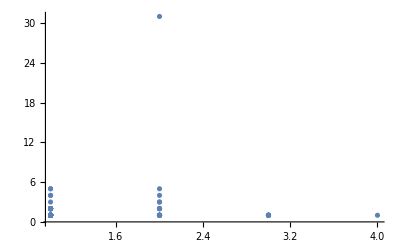

```mathematica
ListPlot[points2]
```